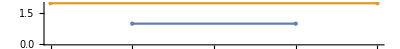

```mathematica
NumberLinePlot[{Interval[{0.25, 0.75}], Interval[{0, 1}]}]
```

```mathematica
Solve[Pi r^2== 0.5, r]
```

{{r→-0.398942},{r→0.398942}}

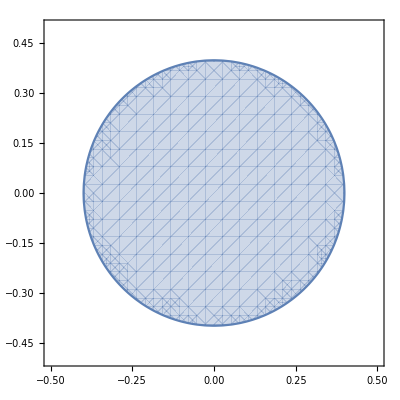

```mathematica
circle = RegionPlot[{x^2 + y^2≤ 0.3989422804014327^2, x==0.5}, {x,-0.5,0.5},{y,-0.5,0.5}]
```

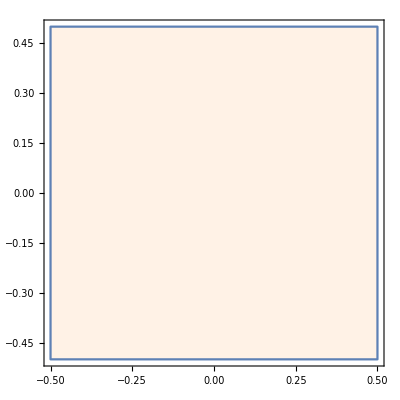

```mathematica
square = RegionPlot[x ≤0.5 && x ≥-0.5 && y<=0.5 && y>= -0.5, {x,-0.5,0.5},{y,-0.5,0.5}, PlotStyle->Lighter[Orange,.9]]
```

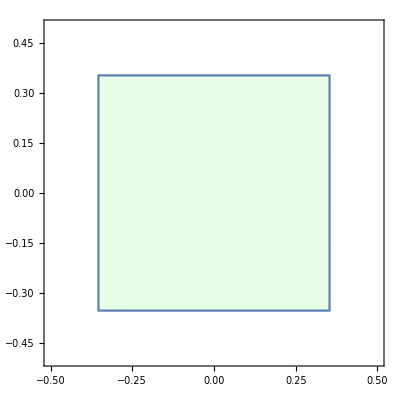

```mathematica
square2 = RegionPlot[x ≤(√0.5)/2 && x ≥(-√0.5)/2 && y≤(√0.5)/2 && y>= (-√0.5)/2, {x,-0.5,0.5},{y,-0.5,0.5}, PlotStyle->Lighter[Green,.9]]
```

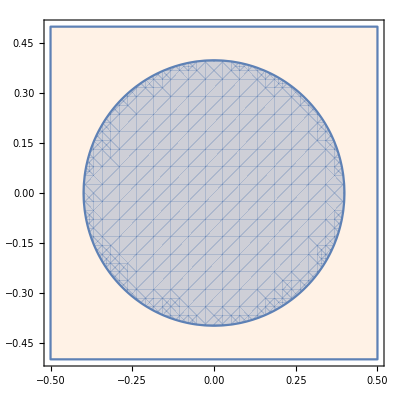

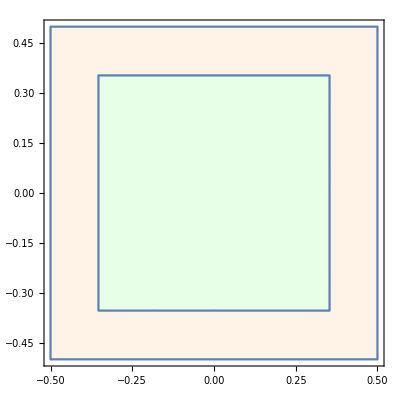

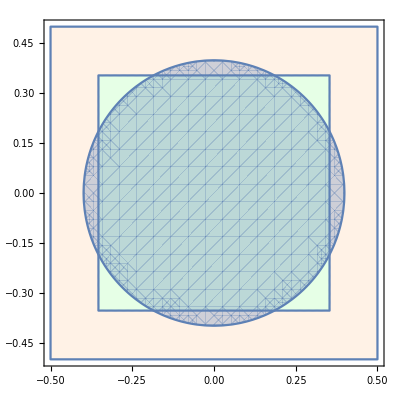

```mathematica
Show[{square, circle}]
Show[{square, square2}]
Show[{square, square2, circle}]
```

```mathematica
Solve[4/3 Pi r^3== 0.5, r]
```

{{r→-0.246186-0.426407 ⅈ},{r→-0.246186+0.426407 ⅈ},{r→0.492373}}

```mathematica
ContourPlot3D[x ≤0.5^(1/3)/2 && x ≥-0.5^(1/3)/2 && y≤0.5^(1/3)/2 && y≥ -0.5^(1/3)/2 && z≤ 0.5^(1/3)/2 && z≥-0.5^(1/3)/2,{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]
```

ContourPlot3D[x≤0.5^(1/3)/2&&x≥-0.5^(1/3)/2&&y≤0.5^(1/3)/2&&y≥-0.5^(1/3)/2&&z≤0.5^(1/3)/2&&z≥-0.5^(1/3)/2,{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]

```mathematica
sphere=ContourPlot3D[x^2+y^2+z^2== 0.49237251092134826^2,{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]
```

-Graphics3D-

```mathematica
cube1 =Graphics3D[{Yellow,Opacity[0.2],Cuboid[{-0.5, -0.5, -0.5},{0.5, 0.5, 0.5}], }]
cube2 = Graphics3D[{Blue,Opacity [0.3],Cuboid[{-(1/2)^(1/3)/2, -(1/2)^(1/3)/2, -(1/2)^(1/3)/2},{(1/2)^(1/3)/2, (1/2)^(1/3)/2, (1/2)^(1/3)/2}]}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[{cube1, sphere}]
```

-Graphics3D-

```mathematica
Show[{cube1, cube2}]
```

```mathematica
Show[cube1, cube2, sphere]
```

-Graphics3D-

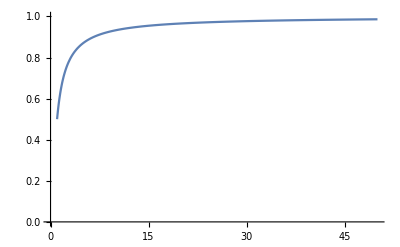

```mathematica
Plot[0.5^(1/x), {x, 1, 50}, PlotRange -> {{0,50},{0, 1}}]
```

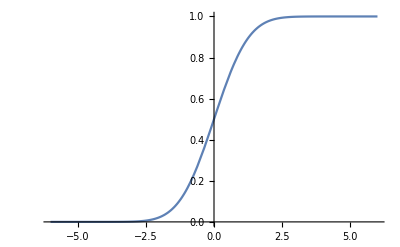

```mathematica
Plot[CDF[NormalDistribution[0,1], x], {x, -6, 6}]
```

```mathematica
Solve[CDF[NormalDistribution[0,1]^2, x]==0.9772498680518208, x] // N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→InverseFunction[CDF,2,2][NormalDistribution[0.,1.]^2,0.97725]}}

```mathematica
CDF[NormalDistribution[0,1], 2] // N
```

0.97725

```mathematica
Needs["Plotly`"]
```